```mathematica
dir="D:\\betterTerrain"
```

D:\betterTerrain

```mathematica
cell=0;
GetAltitude[frameNo_]:=Module[{path,file,headings,items,applyHeading,organisms},
path = StringForm["``\\output\\frame``.csv",dir,frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
Cases[{"pt","y"}/.items,{cell,y_}->y]
]
```

```mathematica
fMin=0;
fMax=700000;
df=10000(*Ceiling[(fMax-fMin)/1000]10;*)
yMax=100;
dy=1;
frames=Table[frame,{frame,fMin,fMax,df}];
data=ParallelMap[BinCounts[GetAltitude[#],{0,yMax,dy}]&,frames];
```

10000

Import::nffil: File not found during Import.

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Rest::normal: Nonatomic expression expected at position 1 in Rest[$Failed].

MapThread::mptd: Object First[$Failed] at position {2, 1} in MapThread[#1→#2&,{First[$Failed],$Failed}] has only 0 of required 1 dimensions.

MapThread::argtu: MapThread called with 1 argument; 2 or 3 arguments are expected.

ReplaceAll::reps: {MapThread[{First[$Failed],$Failed}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

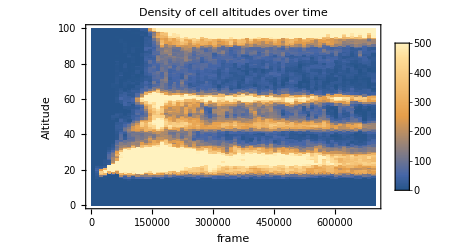

```mathematica
ListDensityPlot[
data//Transpose,
DataRange->{{fMin,fMax},{0,yMax}},
FrameLabel->{"frame","Altitude"},
ClippingStyle->Automatic,
PlotRange->500,
PlotLegends->Placed[Automatic,Right],
InterpolationOrder->0,
AspectRatio->1/GoldenRatio,
PlotLabel->"Density of cell altitudes over time"
]
```

```mathematica
BinCounts[GetAltitude[fMax]]
```

{1,0,0,2,3,2,0,1,0,0,0,0,0,0,0,1,2,0,0,1,1,5,0,0,0,0,2,3,3,1,8,14,26,37,203,464,688,891,10162,9234,2499}

```mathematica
ListPlot3D[
data//Transpose,
DataRange->{{fMin,fMax},{0,yMax}},
AxesLabel->{"frame","Altitude","Density of cell altitudes"},
PlotRange->Full,
BoxRatios->{4,1,1},
ColorFunction->"DarkRainbow"]
```

-Graphics3D-